Painting with Wavelets

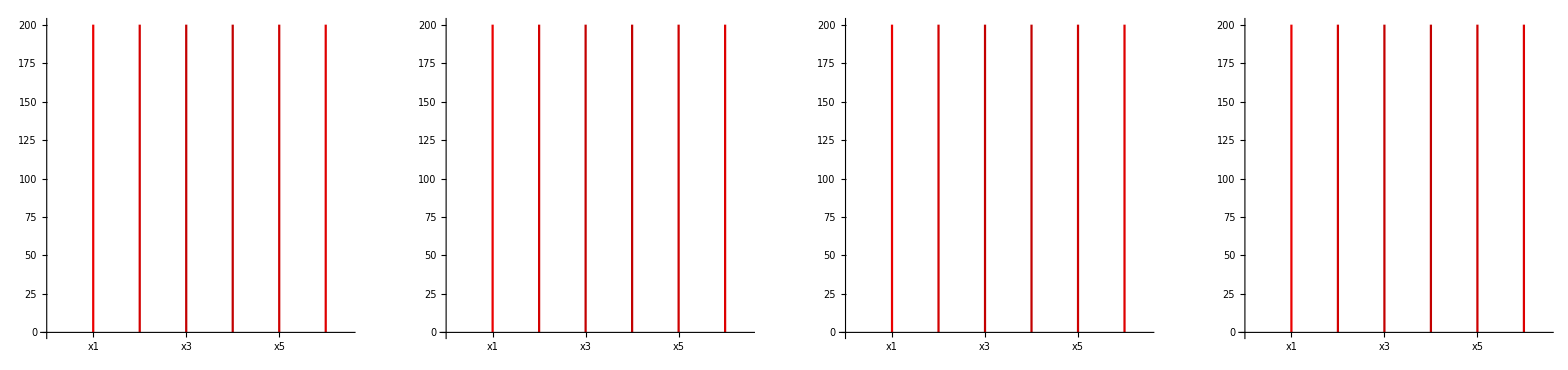

```mathematica
cf[x_]:=Blend[Table[RGBColor[i,0.,0.],{i,0,1,1/50}],x];
a=8;b=18;c=0;m0=-1.296;m1=-0.738;

f1=m1*x1[t]+0.5*(m0-m1)*(Abs[x1[t]+1]-Abs[x1[t]-1]);(*x1-x6是6个不同的位置*)
f2=m1*x2[t]+0.5*(m0-m1)*(Abs[x2[t]+1]-Abs[x2[t]-1]);
f3=m1*x3[t]+0.5*(m0-m1)*(Abs[x3[t]+1]-Abs[x3[t]-1]);
f4=m1*x4[t]+0.5*(m0-m1)*(Abs[x4[t]+1]-Abs[x4[t]-1]);
f5=m1*x5[t]+0.5*(m0-m1)*(Abs[x5[t]+1]-Abs[x5[t]-1]);
f6=m1*x6[t]+0.5*(m0-m1)*(Abs[x6[t]+1]-Abs[x6[t]-1]);
k={0.001,0.005,0.01,0.02};
s=NDSolve[{x1'[t]==a*(y1[t]-x1[t]-f1)+k[[#]] (y6'[t]-x1'[t]),y1'[t]==x1[t]-y1[t]+z1[t]+k[[#]]*(x2'[t]-y1'[t]),z1'[t]==-b*y1[t]-c*z1[t],x2'[t]==a*(y2[t]-x2[t]-f2)+k[[#]] (y1'[t]-x2'[t]),y2'[t]==x2[t]-y2[t]+z2[t]+k[[#]]*(x3'[t]-y2'[t]),z2'[t]==-b*y2[t]-c*z2[t],x3'[t]==a*(y3[t]-x3[t]-f3)+k[[#]] (y2'[t]-x3'[t]),y3'[t]==x3[t]-y3[t]+z3[t]+k[[#]]*(x4'[t]-y3'[t]),z3'[t]==-b*y3[t]-c*z3[t],x4'[t]==a*(y4[t]-x4[t]-f4)+k[[#]] (y3'[t]-x4'[t]),y4'[t]==x4[t]-y4[t]+z4[t]+k[[#]]*(x5'[t]-y4'[t]),z4'[t]==-b*y4[t]-c*z4[t],x5'[t]==a*(y5[t]-x5[t]-f5)+k[[#]] (y4'[t]-x5'[t]),y5'[t]==x5[t]-y5[t]+z5[t]+k[[#]]*(x6'[t]-y5'[t]),z5'[t]==-b*y5[t]-c*z5[t],x6'[t]==a*(y6[t]-x6[t]-f6)+k[[#]] (y5'[t]-x6'[t]),y6'[t]==x6[t]-y6[t]+z6[t]+k[[#]]*(x1'[t]-y6'[t]),z6'[t]==-b*y6[t]-c*z6[t],x1[0]==0.1,y1[0]==0.1,z1[0]==0.01,x2[0]==0.2,y2[0]==0.2,z2[0]==0.02,x3[0]==0.3,y3[0]==0.3,z3[0]==0.03,x4[0]==0.4,y4[0]==0.4,z4[0]==0.04,x5[0]==0.5,y5[0]==0.5,z5[0]==0.05,x6[0]==0.6,y6[0]==0.6,z6[0]==0.06},{x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4,x5,y5,z5,x6,y6,z6},{t,0,200}]&/@Range[4];
(*ColorFunctionScaling->True*)
GraphicsRow@Table[Show@Table[ParametricPlot[{i,t},{t,0,200},ColorFunction->(cf[1/5*(Sum[Sqrt[Sum[(Symbol[k<>ToString[i]][#2]-Symbol[k<>ToString[j]][#2])^2,{k,{"x","y","z"}}]],{j,6}]/.s[[l]])[[1]]]&),ColorFunctionScaling->True,PlotRange->{{0,6.5},{0,200}},AspectRatio->1,Ticks->{{#,"x"<>ToString[#]}&/@Range[6],Automatic}],{i,6}],{l,4}]
```

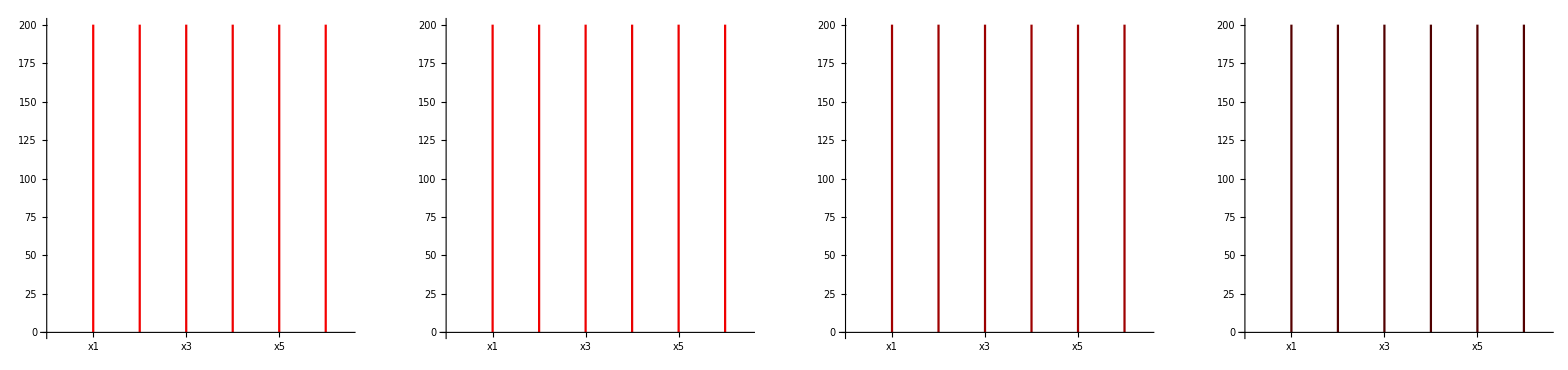

```mathematica
(*ColorFunctionScaling->False*)
GraphicsRow@Table[Show@Table[ParametricPlot[{i,t},{t,0,200},ColorFunction->(cf[1/5*(Sum[Sqrt[Sum[(Symbol[k<>ToString[i]][#2]-Symbol[k<>ToString[j]][#2])^2,{k,{"x","y","z"}}]],{j,6}]/.s[[l]])[[1]]]&),ColorFunctionScaling->False,PlotRange->{{0,6.5},{0,200}},AspectRatio->1,Ticks->{{#,"x"<>ToString[#]}&/@Range[6],Automatic}],{i,6}],{l,4}]
```

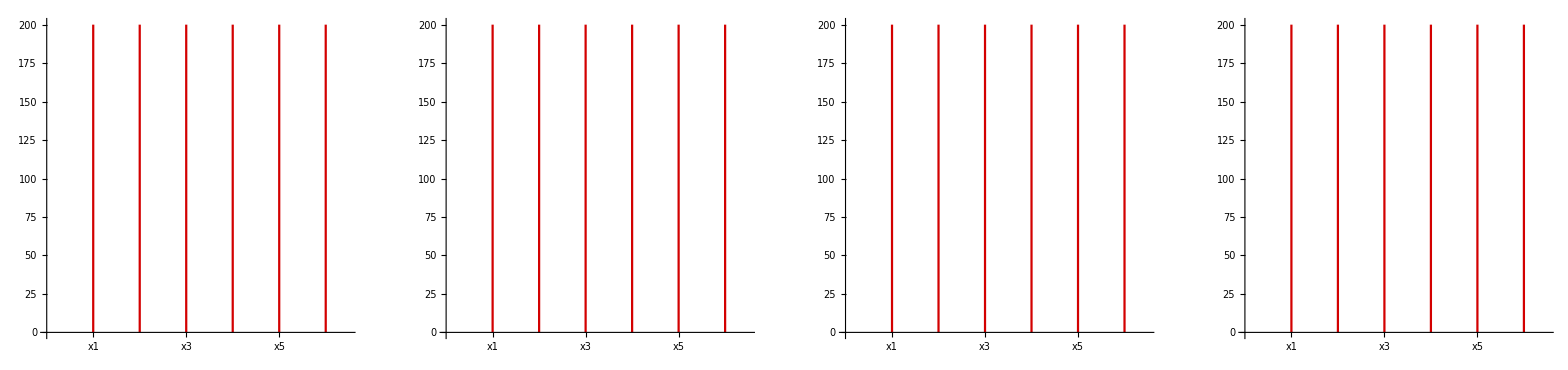

```mathematica
GraphicsRow@Table[Show@Table[ParametricPlot[{i,t},{t,0,200},ColorFunction->(cf[(1/5*(Sqrt[(x2[#2]-x1[#2])^2+(y2[#2]-y1[#2])^2+(z2[#2]-z1[#2])^2]+Sqrt[(x2[#2]-x3[#2])^2+(y2[#2]-y3[#2])^2+(z2[#2]-z3[#2])^2]+Sqrt[(x2[#2]-x6[#2])^2+(y2[#2]-y6[#2])^2+(z2[#2]-z6[#2])^2]+Sqrt[(x2[#2]-x4[#2])^2+(y2[#2]-y4[#2])^2+(z2[#2]-z4[#2])^2]+Sqrt[(x2[#2]-x5[#2])^2+(y2[#2]-y5[#2])^2+(z2[#2]-z5[#2])^2])/.s[[l]])[[1]]]&),ColorFunctionScaling->True,PlotRange->{{0,6.5},{0,200}},AspectRatio->1,Ticks->{{#,"x"<>ToString[#]}&/@Range[6],Automatic}],{i,6}],{l,4}]
```

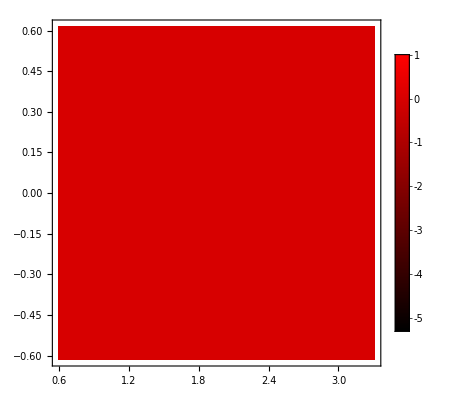

```mathematica
data=Table[{x6[u],y6[v],z6[w]}/.s[[1]][[1]],{u,0,200,5},{v,0,200,5},{w,0,200,5}];
data2=Flatten[data,2];
ListDensityPlot[data2,PlotRange->All,ColorFunctionScaling->True,ColorFunction->(cf[#]&),PlotLegends->Automatic]
```

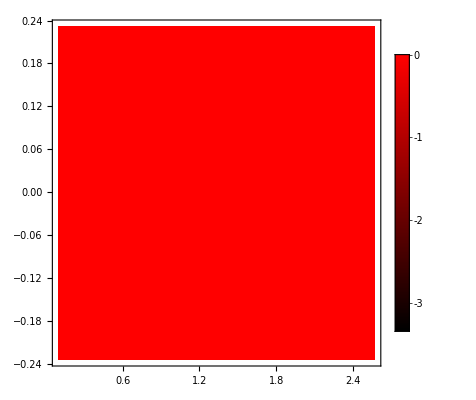

```mathematica
data3=Table[{x1[u],y1[v],z1[w]}/.s[[1]][[1]],{u,0,200,5},{v,0,200,5},{w,0,200,5}];
data4=Flatten[data3,2];
ListDensityPlot[data4,PlotRange->All,ColorFunctionScaling->True,ColorFunction->(cf[#]&),PlotLegends->Automatic]
```

Graphical patterns using wavelets suggest many interesting possibilities for artistic designs. As a basis for this Demonstration I have used the line spectrum of my Demonstrations "Modular Music" and "Modular Interference Diagrams". For coloring, I suggest using some built-in palettes that are very effective for the visualization of wavelets from the aesthetic point of view.

Suggestion: search for a periodic and symmetric pattern in the line spectrum and compare it with the result of the wavelet transformation.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Wavelet

Signal Processing

Modular Music

Modular Interference Diagrams

Contributed by: Herbert W. Franke